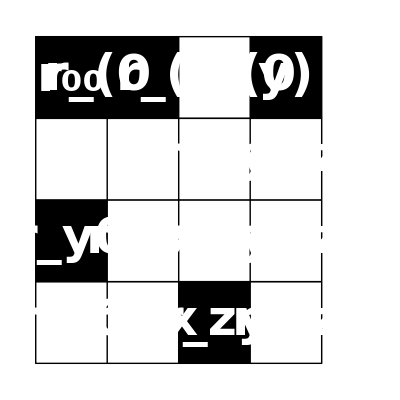

```mathematica
Graphics[{{Black,EdgeForm[Directive[Black,Thick]],Rectangle[{0,1},{4,-3}]},
{Black,EdgeForm[Directive[Black,Thick]],Rectangle[{0,0},{1,1}]},{Black,EdgeForm[Directive[Black,Thick]],Rectangle[{1,0},{4,1}]},{Black,EdgeForm[Directive[Black,Thick]],Rectangle[{0,0},{1,-3}]},
{Black,EdgeForm[Directive[Black,Thick]],Rectangle[{1,0},{4,-3}]},
{White,Text[Style["r_00",Bold,FontSize->50],{0.5,0.5}]},
{White,Text[Style["r_(0  x)",Bold,FontSize->50],{1.5,0.5}]},
{White,Text[Style["r_(0  y)",Bold,FontSize->50],{2.5,0.5}]},
{White,Text[Style["r_(0  z)",Bold,FontSize->50],{3.5,0.5}]},
{White,Text[Style["r_x0",Bold,FontSize->50],{0.5,-0.5}]},
{White,Text[Style["r_y0",Bold,FontSize->50],{0.5,-1.5}]},
{White,Text[Style["r_z0",Bold,FontSize->50],{0.5,-2.5}]},
{White,Text[Style["r_xx",Bold,FontSize->50],{1.5,-0.5}]},
{White,Text[Style["r_xy",Bold,FontSize->50],{2.5,-0.5}]},
{White,Text[Style["r_xz",Bold,FontSize->50],{3.5,-0.5}]},
{White,Text[Style["r_yx",Bold,FontSize->50],{1.5,-1.5}]},
{White,Text[Style["r_yy",Bold,FontSize->50],{2.5,-1.5}]},
{White,Text[Style["r_yz",Bold,FontSize->50],{3.5,-1.5}]},
{White,Text[Style["r_zx",Bold,FontSize->50],{1.5,-2.5}]},
{White,Text[Style["r_zy",Bold,FontSize->50],{2.5,-2.5}]},
{White,Text[Style["r_zz",Bold,FontSize->50],{3.5,-2.5}]},
Black,Thickness[.02],Line[{{2,0.98},{2,-2.98}}],
Black,Thickness[.02],Line[{{3,0.97},{3,-2.97}}],
Black,Thick,Line[{{0.03,-1},{3.97,-1}}],
Black,Thick,Line[{{0.03,-2},{3.97,-2}}],
White,Rectangle[{0.01,-0.01},{.99,-.99}],
White,Rectangle[{1.01,-0.01},{1.99,-.99}],
White,Rectangle[{3.01,-0.01},{3.99,-.99}],
White,Rectangle[{2.01,0.01},{2.99,.99}],
White,Rectangle[{0.01,-2.01},{.99,-2.99}],
White,Rectangle[{1.01,-1.01},{1.99,-1.99}],
White,Rectangle[{2.01,-1.01},{2.99,-1.99}],
White,Rectangle[{3.01,-1.01},{3.99,-1.99}],
White,Rectangle[{3.01,-2.01},{3.99,-2.99}],
White,Rectangle[{1.01,-2.01},{1.99,-2.99}],
White,Rectangle[{2.01,-.01},{2.99,-.99}]
},Frame->None
]
```

```mathematica
{White,Rectangle[{0,0},{3,-2}]},
White,Rectangle[{3,-2},{4,-3}],
```

```mathematica
Graphics[{{EdgeForm[Thick],Black,Rectangle[{0,0},{1,-1}]},
Black,{EdgeForm[Thick],Rectangle[{0,-1},{1,-4}]},
White,{EdgeForm[Thick],Rectangle[{0,-3},{1,-4}]},
White,Text[Style["r_0",Bold,FontSize->35],{0.5,-0.5}],
White,Text[Style["r_x",Bold,FontSize->35],{0.5,-1.5}],
White,Text[Style["r_y",Bold,FontSize->35],{0.5,-2.5}],
White,Thick,Line[{{0,-1},{1,-1}}],
White,Thick,Line[{{0,-2},{1,-2}}],
White,Thick,Line[{{0,-3},{1,-3}}]}]
```

-Graphics-

```mathematica
Graphics3D[{Black,Cuboid[{-0.5,-0.5,-0.5},{0.5,0.5,0.5}],
RGBColor["#CC0000"],Cuboid[{-0.5,0.5,0.5},{0.5,3.5,-0.5}],
RGBColor["#CC0000"],Cuboid[{0.5,-0.5,0.5},{3.5,0.5,-0.5}],
RGBColor["#CC0000"],Cuboid[{0.5,0.5,0.5},{-0.5,-0.5,3.5}],
RGBColor["#004C99"],Cuboid[{0.5,0.5,0.5},{-0.5,3.5,3.5}],
RGBColor["#004C99"],Cuboid[{0.5,0.5,0.5},{3.5,-0.5,3.5}],
RGBColor["#004C99"],Cuboid[{0.5,0.5,0.5},{3.5,3.5,-0.5}],
RGBColor["#99FF33"],Cuboid[{0.5,0.5,0.5},{3.5,3.5,3.5}]},Axes->False,AxesLabel->{x,y,z},LabelStyle->Directive[Bold, Large,White],PlotRange->{{-0.5,3.5},{-0.5,3.5},{-0.5,3.5}},AxesOrigin->{0.5,0.5,0.5},AxesStyle->Thickness[0.01]]
```

-Graphics3D-

```mathematica
Solve[n^3==3.5(36+12n+n^2),n]//FullSimplify
```

{{n→-2.94833-2.17171 ⅈ},{n→-2.94833+2.17171 ⅈ},{n→9.39667}}

```mathematica
SparseArray[{{1,4},{3,6},{5,2}}->{a,b,c},{6,6}]//Normal//MatrixForm
```

(0 | 0 | 0 | a | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | b
0 | 0 | 0 | 0 | 0 | 0
0 | c | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)